```mathematica
Clear["Global`*"];
```

```mathematica
Clear["Global`*"];
nc=3; ω=0.02280;E0=0.05338;ξ=0;Ip=0.5792;
p0z=-2;p0x=0.0202020;ts0=200+50I;
tp=2 Pi nc/ω;
AFz[t_]:=-E0/(ω √(1+ξ^2)) Sin[(ω t)/(2 nc)]^2 Sin[ω t ]
AFx[t_]:=-(E0 ξ)/(ω √(1+ξ^2)) Sin[(ω t-Pi/2)/(2 nc)]^2 Cos[ω t ]
EFz[t_]:=-D[(AFz[τ]), τ]/.τ->t
EFx[t_]:=-D[(AFx[τ]), τ]/.τ->t
alphaz[t_]:=∫_t0^t AFz[τ]ⅆτ
alphax[t_]:=∫_t0^t AFx[τ]ⅆτ

ts=τ/.FindRoot[(AFz[τ]+p0z)^2+(AFx[τ]+p0x)^2+2Ip==0,{τ, ts0}]
t0=Re[ts]
vz[t_]:=p0z+AFz[t]
vx[t_]:=p0x+AFx[t]
z[t_]:=alphaz[t]+p0z t-Re[alphaz[ts]]-Re[p0z ts]
x[t_]:=alphax[t]+p0x t-Re[alphax[ts]]-Re[p0x ts]
```

202.332+53.7033 ⅈ

202.332

```mathematica
AFz[ts0]
AFx[ts0]
EFz[ts0]
EFx[ts0]
alphaz[ts0]
alphax[ts0]
ts
t0
vz[ts]
vx[ts]
z[ts]
x[ts]
```

1.78835+1.01087 ⅈ

0

-0.0371962+0.0299626 ⅈ

0

-22.9408+66.0282 ⅈ

0

202.332+53.7033 ⅈ

202.332

4.44089×10^-16+1.07648 ⅈ

0.020202

0.-31.9373 ⅈ

0.+1.08491 ⅈ

{{xx→InterpolatingFunction[{{202.332,826.735}},<>],zz→InterpolatingFunction[{{202.332,826.735}},<>]}}

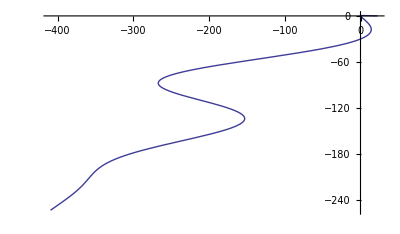

{{-252.945,-409.323}}

```mathematica
s=NDSolve[{xx''[t]==-EFx[t]-xx[t]/(xx[t]^2+zz[t]^2)^(3/2),zz''[t]==-EFz[t]-zz[t]/(xx[t]^2+zz[t]^2)^(3/2),xx[t0]==x[t0],zz[t0]==z[t0],xx'[t0]==vx[t0],zz'[t0]==vz[t0]},{xx,zz},{t,t0,tp}]
ParametricPlot[Evaluate[{zz[t],xx[t]}/.s],{t,t0,tp}]
{xx[tp], zz[tp]}/.s
```